```mathematica
Get["invariant_dmd_v2_8_functions"];
Get["invariant_dmd_v2_8_auxuntested_v1"];
```

```mathematica
Get["dslibrary_v3_3"];
```

## Savefile

```mathematica
savefile = "cubicstable_pruned_v1";
```

## Temporal parameters

0 usually - If delayed, set appropriately

```mathematica
ndelays = 0;

tinit = 0;
tsamp = 0.1;
```

#### Choice of DS

```mathematica
(* Create a separate one for each DS*)
rvalues = {-1/2,2/10,7/10};
localcubicstable1D[t_,{r_}]:=cubicstable1D[t,{r},rvalues];
vfield = localcubicstable1D;
(* chosenputty: Use to convert coordinates from the ODE version *)
chosenputty = #& ;
```

### Tolerances

```mathematica
(* Tolerance *)
sigtols = {10^-8,10^-12}; (* Singular values *)
restols = {10^-8,10^-12};(* greaterabsrelcheck *)
```

### Flavours

#### User defined functions

```mathematica
(* AppendTo[userlist,(*Desired fheads*)];*)
userparams = {};
```

#### User defined constraints

Should be a LIST of matrices !!!

```mathematica
(* Geometric constraints *)
invsamplesets ;
(* Functional constraints *)
ipfuns(**);
opfuns(**);
rawuserlist = {};
```

#### Test constraints

```mathematica
testinvsamplesets =  N@getcubicstable1Dinvsamplesets[rvalues];
(*------Typically, left unused as we are only including the constant ef, which has it's own way------*)
testipfuns;
testopfuns;
```

```mathematica
flavour = "boxfuns";
boxranges = {{-1,1}};
centercounts = {{61},{61}(* Must be the same as the first to ensure that the scaling is correctly done for trigtri *)};
nsampsperbox = {101,11};



(* How muich of the fringe be included in the plots*)
plotscalefactor = 1.1;
```

## Must use this version !!!!

```mathematica
icsconwrap4modifiedoneshot[ics_,{{construct_,basistruct_,invsamplesets_,testinvsamplesets_},{userparams_,rawuserlist_,ipfuns_,opfuns_,testipfuns_,testopfuns_}}]:=modifiedoneshot[ndelays,tinit,tsamp,vfield,ics,chosenputty,sigtols,restols,flavour,flavourparams,construct,basistruct,userparams,rawuserlist,invsamplesets,ipfuns,opfuns,testinvsamplesets,testipfuns,testopfuns,boxflavourparams];
```

## Actual test

#### Sample points

```mathematica
boxflavourparams = {boxranges,centercounts[[-1]]};
flavourparams ={boxranges,centercounts[[1]]};
```

```mathematica
detics = N@Join@@MapThread[(#1@(getdetseeds4Box[boxranges,#2,#3]))&,{{#&,puttheseoutright[#,boxflavourparams]&},centercounts,nsampsperbox}];
ncompsamples = Length@detics;
```

#### Plot points

```mathematica
plotcc = centercounts[[1]];
plotspb = nsampsperbox[[1]];
plotbrs  = plotscalefactor *boxranges;
plotparams = {plotbrs,plotcc,plotspb};
(*----------ODE in sampled coordinates ----------*)
plotics = N@getdetseeds4Box@@plotparams;
```

#### Expected spectrum

```mathematica
jacobevals =FunctionExpand@Flatten@Map[N@Eigenvalues@getjacobian[(*Vector field *)vfield,{t,#}]&,(*fixedpoints*)Flatten[testinvsamplesets,1]];
expectedevalues  = Exp[jacobevals*tsamp];
```

### Le test variations

Switches for the constant eigenfunction && the delay constraints (You need to put the constant function in userhead !!!) : Set True to activate

```mathematica
neededbaggage = {detics,plotics,sigtols,tsamp,ncompsamples,ndelays,flavourparams,expectedevalues};
```

```mathematica
activecons;
passivecons = {userparams,rawuserlist,ipfuns,opfuns,testipfuns,testopfuns};
```

```mathematica
goodplotgrub=MapThread[getcrunchedata[{#1,#2,#3,testinvsamplesets},passivecons,neededbaggage]&,{{True,True,False},{True,True,False},{testinvsamplesets,{},{}}}];
DumpSave[savefile,{goodplotgrub,plotparams}];
```

{0.1,6831,0,{{{-1,1}},{61}},{6.44362,0},{{1.25324×10^-15,1.20858×10^-14},{1.20422×10^-15,1.20422×10^-15}},225.615}

{0.1,6831,0,{{{-1,1}},{61}},{6.77326,0},{{0.0278968,0.265671},{1.59043×10^-15,1.59043×10^-15}},225.599}

{0.1,6831,0,{{{-1,1}},{61}},{1.,0},{{0.02837,0.265671},{}},225.65}

#### {testamat,ploticslifted,testefgrubvecs} ⟶ Meaning of goodplotgrub here for the correct plots to happen

```mathematica
Quit[];
```

### Plots

```mathematica
(* Also fetch all functions in auxuntested_v1 *)
Get["invariant_dmd_v2_8_functions"];
Get["invariant_dmd_v2_8_auxuntested_v1"];
(* Typically file name is stored in savefile *)
Get["cubicstable_pruned_v1"];
```

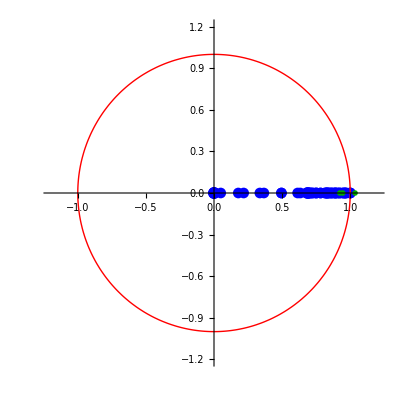
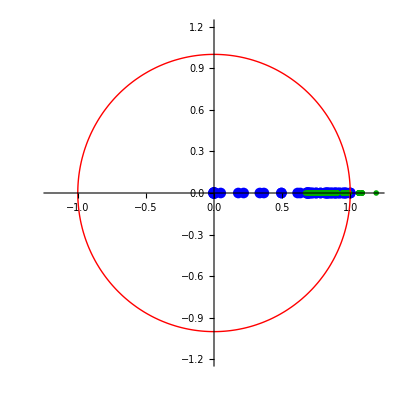

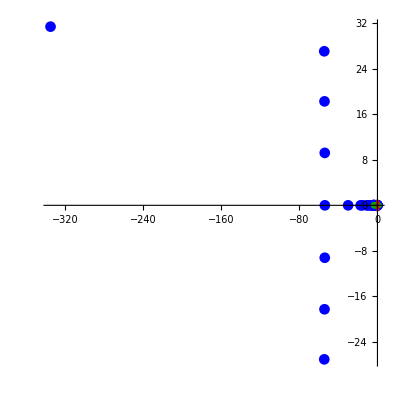

```mathematica
plotics =visualizespectrum [goodplotgrub[[1]],plotparams];
```

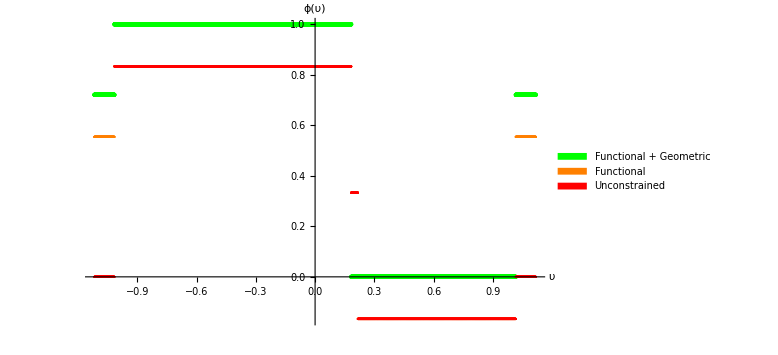
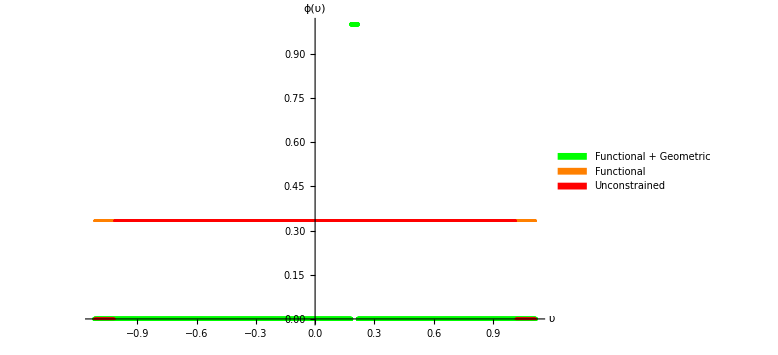
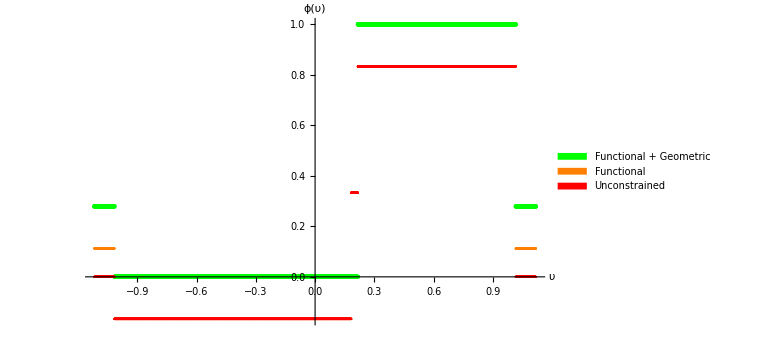

```mathematica
plotcolourscheme = {Directive[Green,PointSize[Medium]],Orange,Red};
plotlegendscheme = {Green,Orange,Red};
efplots =Table[ListPlot[Map[getlistplotdata[#[[3,i,1]],N@plotics,#[[2]],#&]&,goodplotgrub[[All,Range[3]]]],PlotRange->All,PerformanceGoal->"Quality",PlotStyle->plotcolourscheme,AxesLabel->{"υ","ϕ(υ)"},LabelStyle->Directive[Bold,Black,Medium],ImageSize->Large,PlotLegends->SwatchLegend[plotlegendscheme ,{"Functional + Geometric","Functional","Unconstrained"}]],{i,3}]
```